# Determining the first order phase transition for λ=0.

We will define the functions the same as we have done for the files “1) Topological Phase transition” and “2) Non 0 Magnetisation”.

```mathematica
Clear[kx];
Clear[ky];
n1[kx_,ky_]:=-kx*Sqrt[3]/2+(3/2)*ky
n2[kx_,ky_]:=kx*Sqrt[3]/2+(3/2)*ky
gamma0mag[Cp_,Cz_,kx_,ky_]:= Sqrt[(Cz+Cp*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2 + (Cp*(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2]

gammaZmag[Bp_,Bz_,P1_,P_,K1_,kx_,ky_] := Sqrt[((1+P+K1*(1+P1))*Bz+Bp*K1*(1+P1)*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2+(Bp*K1*(1+P1)*(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2]

gammaXmag[P1_,K1_,Bp_,Bz_,kx_,ky_] := Sqrt[(Bp((1+K1)*Cos[n1[kx,ky]]+K1*Cos[n2[kx,ky]])+K1*Bz)^2 +(Bp*((1+K1)*Sin[n1[kx,ky]]+K1*Sin[n2[kx,ky]]))^2]

gammaYmag[P1_,K1_,Bp_,Bz_,kx_,ky_] := Sqrt[(Bp((1+K1)*Cos[n2[kx,ky]]+K1*Cos[n1[kx,ky]])+K1*Bz)^2 +(Bp*((1+K1)*Sin[n2[kx,ky]]+K1*Sin[n1[kx,ky]]))^2]

E0[P1_,K1_,P_,M_,Bp_,Bz_,a1_,a2_]:=2*Bp*a1+Bz*a2+M^2/(3K1*(1+P1)+1+P)

gamma0Zmag2[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,kx_,ky_] :=(Cz-(1+P+K1*(1+P1))*Bz+(Cp-Bp*K1*(1+P1))*(Cos[n1[kx,ky]]+Cos[n2[kx,ky]]))^2+((Cp-Bp*K1(1+P1))(Sin[n1[kx,ky]]+Sin[n2[kx,ky]]))^2

gammaXYmag2[Bp_,kx_,ky_]:= (Bp(Cos[n1[kx,ky]]-Cos[n2[kx,ky]]))^2+(Bp(Sin[n1[kx,ky]]-Sin[n2[kx,ky]]))^2

eigen1[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:= Sqrt[(gamma0mag[Cp,Cz,kx,ky]^2+gammaZmag[Bp,Bz,P1,P,K1,kx,ky] ^2)/2 + (M-L)^2 + 
Sqrt[((gamma0mag[Cp,Cz,kx,ky]^2-gammaZmag[Bp,Bz,P1,P,K1,kx,ky]^2 )/2 )^2+((M-L)^2)*gamma0Zmag2[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky]]];

eigen2[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:= Sqrt[(gamma0mag[Cp,Cz,kx,ky]^2+gammaZmag[Bp,Bz,P1,P,K1,kx,ky] ^2)/2 + (M-L)^2 - 
Sqrt[((gamma0mag[Cp,Cz,kx,ky]^2-gammaZmag[Bp,Bz,P1,P,K1,kx,ky]^2 )/2 )^2+((M-L)^2)*gamma0Zmag2[P1,P,K1,Cp,Cz,Bp,Bz,kx,ky]]];

eigen3[P1_,K1_,Bp_,Bz_,L_,kx_,ky_]:=Sqrt[(gammaXmag[P1,K1,Bp,Bz,kx,ky]^2+gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2+L^2+
Sqrt[((gammaXmag[P1,K1,Bp,Bz,kx,ky]^2-gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2)^2+L^2*gammaXYmag2[Bp,kx,ky]]];

eigen4[P1_,K1_,Bp_,Bz_,L_,kx_,ky_]:=Sqrt[(gammaXmag[P1,K1,Bp,Bz,kx,ky]^2+gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2+L^2-
Sqrt[((gammaXmag[P1,K1,Bp,Bz,kx,ky]^2-gammaYmag[P1,K1,Bp,Bz,kx,ky]^2)/2)^2+L^2*gammaXYmag2[Bp,kx,ky]]];

Clear[P1];
Clear[P];
Clear[K1];
Clear[M];
Clear[L];
(*Simplify[Eigensum[P1,P,K1,Cp,Cz,Bp,Bz,M,L,kx,ky]]*)
Eigensum[P1_,P_,K1_,Cp_,Cz_,Bp_,Bz_,M_,L_,kx_,ky_]:=1/(√2)(√2 √(Bp^2+2 Bp^2 K1+2 Bp^2 K1^2+Bz^2 K1^2+L^2+2 Bp^2 K1 (1+K1) Cos[√3 kx]+2 Bp Bz K1 (1+2 K1) Cos[(√3 kx)/2] Cos[(3 ky)/2]-√(Bp^2 (-1+Cos[√3 kx]) (-Bz^2 K1^2-2 L^2+Bz^2 K1^2 Cos[3 ky])))+√2 √(Bp^2+2 Bp^2 K1+2 Bp^2 K1^2+Bz^2 K1^2+L^2+2 Bp^2 K1 (1+K1) Cos[√3 kx]+2 Bp Bz K1 (1+2 K1) Cos[(√3 kx)/2] Cos[(3 ky)/2]+√(Bp^2 (-1+Cos[√3 kx]) (-Bz^2 K1^2-2 L^2+Bz^2 K1^2 Cos[3 ky])))+√(2 (L-M)^2+(Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-2 √(1/4 ((Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2-(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)^2+(L-M)^2 ((Cz-Bz (1+K1+P+K1 P1)+2 (Cp-Bp K1 (1+P1)) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 (Cp-Bp K1 (1+P1))^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)))+√(2 (L-M)^2+(Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2+2 √(1/4 ((Cz+2 Cp Cos[(√3 kx)/2] Cos[(3 ky)/2])^2-(Bz (1+K1+P+K1 P1)+2 Bp K1 (1+P1) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 Cp^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2-4 Bp^2 K1^2 (1+P1)^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2)^2+(L-M)^2 ((Cz-Bz (1+K1+P+K1 P1)+2 (Cp-Bp K1 (1+P1)) Cos[(√3 kx)/2] Cos[(3 ky)/2])^2+4 (Cp-Bp K1 (1+P1))^2 Cos[(√3 kx)/2]^2 Sin[(3 ky)/2]^2))))

E0[P1_,K1_,P_,M_,Bp_,Bz_,a1_,a2_]:=2*Bp*a1+Bz*a2+M^2/(3K1*(1+P1)+1+P)
Energy [P1_,P_,K1_,A1_,A2_,Bp_,Bz_,M_,L_]:= -1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[Eigensum[P1,P,K1,A1,A2,Bp,Bz,M,L,kx,ky],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}])+E0[P1,K1,P,M,Bp,Bz,A1,A2]

FBp[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]],cz[[i]],Bp,bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Bp]/. Bp->bp[[i]]);
FBz[kx_,ky_,i_]:= (D[Eigensum[P1,P,K1,cp[[i]],cz[[i]],bp[[i]],Bz,m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Bz]/. Bz->bz[[i]]);
FA1[kx_,ky_,i_]:= (D[Eigensum[P1,P,K1, Cp,cz[[i]],bp[[i]],bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Cp]/. Cp->cp[[i]]);
FA2[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]], Cz,bp[[i]],bz[[i]],m[[i]]*(3K1*(1+P1)+1+P),l[[i]],kx,ky],Cz]/. Cz->cz[[i]]);
FM[kx_,ky_,i_]:=(D[Eigensum[P1,P,K1,cp[[i]], cz[[i]],bp[[i]],bz[[i]],M,l[[i]],kx,ky],M]/. M->m[[i]]*(3K1*(1+P1)+1+P));
```

# Convergence checker

```mathematica
cpi=1;
czi=1;
bpi=0.5;
bzi=0.5;
li=0;
```

$Aborted

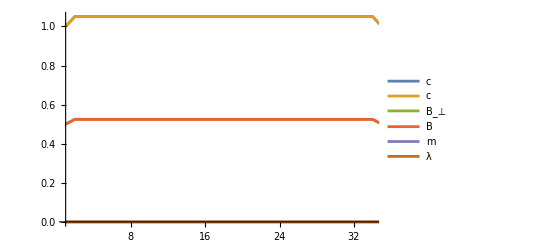

Final MFT Parameters:c_⊥ =1.05119, c_z=1.05119, B_⊥=0.524865TraditionalForm`0.524882, M=0., m=0., λ=0

```mathematica
loop=90;
Clear[cp];
Clear[cz];


cp= ConstantArray[cpi,loop];
cz = ConstantArray[czi,loop];
bp=ConstantArray[bpi,loop];
bz=ConstantArray[bzi,loop];
m=ConstantArray[0.0,loop];
l=ConstantArray[0,loop];
P1=0;
P=0;
K1=0.05;
For[i=1,i<loop,i++,

final=i;

(*other MFT variables*)
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBp [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBp[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);
cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBz[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+
NIntegrate[FBz[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FA1[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FA1[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FA1[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FA2[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FA2[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FA2[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);


];



ListLinePlot[{cp,cz,bp,bz,m,l},PlotLegends->{"c","c","B_⊥","B","m","λ"},PlotRange->{{1,final},Automatic}]
Print["Final MFT Parameters:","c_⊥ =",cp[[final]] ,", c_z=",cz[[final]],", B_⊥=", bp[[final]],"TraditionalForm`", bz[[final]], ", M=", m[[final]]*(3K1*(1+P1)+1+P),", m=", m[[final]], ", λ=", l[[final]]]
z=final-1;
(*Print["Penultimate MFT Parameters:","c_⊥ =",cp[[z]] ,", c_z=",cz[[z]] ,", B_⊥=", bp[[z]],"TraditionalForm`", bz[[z]], ", M=", m[[z]]*(3K1*(1+P1)+1+P),", m=", m[[z]], ", λ=", l[[z]]]*)
```

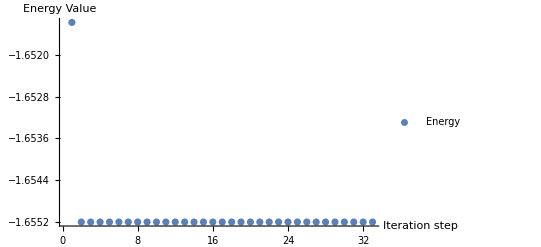

-1.6552

```mathematica
Energyval=ConstantArray[0,final-1];
For[n=1,n<final,n++,
Energyval[[n]] = Energy [P1,P,K1,cp[[n]],cz[[n]],bp[[n]],bz[[n]], m[[n]]*(3K1*(1+P1)+1+P),l[[n]]]
]
ListPlot[Energyval,PlotRange->Full,PlotLegends->{"Energy"}, AxesLabel->{"Iteration step", "Energy Value"}]
Print[Energyval[[final-1]]]
```

# Free energy diagram

```mathematica
cpi=1;
czi=1;
bpi=0.5;
bzi=0.5;
li=0;
```

```mathematica
loop=20;
Clear[cp];
Clear[cz];
li=0;
P1=0;
P=0;
K1=0.07373046875000003;


mag = Range[0,0.95,.05];
Storedvalue = ConstantArray[0,Length[mag]];
Print[Length[mag]];

For[k=1,k<=Length[mag],k++,

cp= ConstantArray[cpi,loop];
cz = ConstantArray[czi,loop];
bp=ConstantArray[bpi,loop];
bz=ConstantArray[bzi,loop];
m=ConstantArray[mag[[k]],loop];
l=ConstantArray[0,loop];
(*Start MFT calc*)
For[i=1,i<loop,i++,
final=i;
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FBp [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FBp[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FBz[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+
NIntegrate[FBz[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FA1[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FA1[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FA1[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FA2[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FA2[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FA2[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

];
(*End MFT calc*)


Storedvalue[[k]]={cp[[final]],cz[[final]], bp[[final]],bz[[final]],mag[[k]],0}

]
```

20

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

## Plotting free energy

We have stored the value of MFT parameters for the free energy given different magnetisation values for κ=0.7545, ρ=0,  ρ̃=0.

```mathematica
Storedvaluex={{1.0780987862248712,1.0780996511851173,0.524855933678354,0.5248816920957572,0.,0},{1.0781783571834314,1.0762657821827015,0.5243860401884798,0.5240285272951777,0.05,0},{1.078414902167171,1.070699092653528,0.5228232549153893,0.5217885394003549,0.1,0},{1.0788386940550756,1.061237962548828,0.5202569718494694,0.5178662487333295,0.15000000000000002,0},{1.0793939312434973,1.047564290754887,0.5166758741002957,0.5122488232101349,0.2,0},{1.080183262200837,1.0292374631768566,0.512101710191915,0.5047624554100173,0.25,0},{1.0811626301627382,1.0055945474470327,0.5065302157994461,0.49519811622758847,0.30000000000000004,0},{1.0824528737597376,0.975660484380109,0.4999835929203873,0.483179277010218,0.35000000000000003,0},{1.084024052930985,0.9379774667570736,0.4924682415571796,0.4681959174790736,0.4,0},{1.0861230519109084,0.8901015056918098,0.4840345903539515,0.4492674404065524,0.45,0},{1.088852714132644,0.8273358366165351,0.4747154575711713,0.4245790103837228,0.5,0},{1.0928546176996143,0.7375188672252369,0.4646970649193548,0.3892045896181618,0.55,0},{1.0987051501438385,0.6016370322439971,0.45540752221035163,0.33157309262362206,0.6000000000000001,0},{1.1034957692233414,0.45510048792860314,0.4475569457530887,0.25838414908404395,0.65,0},{1.1067843632106595,0.3021660241940617,0.4385721375615664,0.1763741105218708,0.7000000000000001,0},{1.107993534760129,0.17408332255992193,0.42719594378157344,0.10462611173902218,0.75,0},{1.1077512301210253,0.09083930816123909,0.41419085919452453,0.05624537134866817,0.8,0},{1.1069476979455306,0.04530077090215827,0.4008155971441945,0.02885652456864335,0.8500000000000001,0},{1.1060107596625088,0.022349063395825895,0.3877198764670162,0.014612985966663649,0.9,0},{1.1050721267392698,0.011097235130382088,0.3751155666883263,0.007430128189320997,0.95,0}};
```

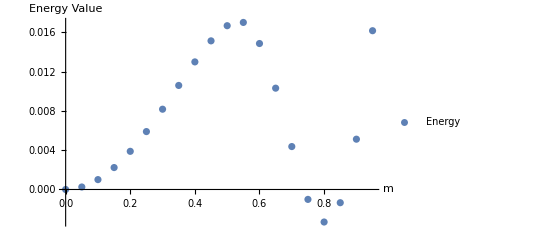

```mathematica
P1=0; 
P=0;
K1=0.07545;
Energyval=ConstantArray[0,Length[Storedvaluex]];
For[n=1,n<=Length[Storedvaluex],n++,
Energyval[[n]] = Energy [P1,P,K1,Storedvaluex[[n]][[1]],Storedvaluex[[n]][[2]],Storedvaluex[[n]][[3]],Storedvaluex[[n]][[4]], Storedvaluex[[n]][[5]]*(3K1*(1+P1)+1+P),0] -Energy [P1,P,K1,Storedvaluex[[1]][[1]],Storedvaluex[[1]][[2]],Storedvaluex[[1]][[3]],Storedvaluex[[1]][[4]], Storedvaluex[[1]][[5]]*(3K1*(1+P1)+1+P),0];

]

ListPlot[Transpose[{Transpose[Storedvaluex][[5]],Energyval}],PlotRange->Full,PlotLegends->{"Energy"}, AxesLabel->{"m", "Energy Value"}]
```

```mathematica
-1.6548373819085087
-1.6552007862818854
```

# Creating a code to produce a series of plots:

```mathematica
cpi=1;
czi=1;
bpi=0.5;
bzi=0.5;
li=0;
loop=10;
Clear[cp];
Clear[cz];
li=0;
P1=0;
P=0;

kappa={0,0.05,0.07545,0.085};
mag1 = Range[0,0.9,.05];
mag2 = Range[0.91,0.96,.01];
mag = Join[mag1,mag2];
Storedvalue = ConstantArray[0,Length[mag]];
Print[Length[mag]];

EnergyPlot = ConstantArray[0,Length[kappa]];

(*Loop over different kappa values*)
For[z=1,z<=Length[kappa],z++,
K1=kappa[[z]];
(*Loop over each magnetisation value*)
For[k=1,k<=Length[mag],k++,
cp= ConstantArray[cpi,loop];
cz = ConstantArray[czi,loop];
bp=ConstantArray[bpi,loop];
bz=ConstantArray[bzi,loop];
m=ConstantArray[mag[[k]],loop];
l=ConstantArray[0,loop];
(*Start MFT calc*)
For[i=1,i<loop,i++,
final=i;
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FBp [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FBp[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FBz[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+
NIntegrate[FBz[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FA1[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FA1[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FA1[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FA2[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FA2[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FA2[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

];
(*End MFT calc*)
Storedvalue[[k]]={cp[[final]],cz[[final]], bp[[final]],bz[[final]],mag[[k]],0};

];

Energyval=ConstantArray[0,Length[Storedvalue]];
(*loop to find the different curves*)
For[n=1,n<=Length[Storedvalue],n++,
Energyval[[n]] = Energy [P1,P,K1,Storedvalue[[n]][[1]],Storedvalue[[n]][[2]],Storedvalue[[n]][[3]],Storedvalue[[n]][[4]], Storedvalue[[n]][[5]]*(3K1*(1+P1)+1+P),0] -Energy [P1,P,K1,Storedvalue[[1]][[1]],Storedvalue[[1]][[2]],Storedvalue[[1]][[3]],Storedvalue[[1]][[4]], Storedvalue[[1]][[5]]*(3K1*(1+P1)+1+P),0];

];

Print[Energyval];
EnergyPlot[[z]]=Energyval;
]
```

25

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.,0.000542216,0.00216242,0.00485162,0.00858444,0.0133292,0.0190436,0.0256732,0.0331482,0.0413835,0.0502708,0.0596611,0.0693638,0.0790751,0.08829,0.0963361,0.103813,0.111501,0.120348,0.122349,0.124446,0.126648,0.12896,0.13139,0.133945}

{0.,0.000363404,0.00144402,0.00322583,0.00567002,0.00871733,0.0123025,0.0163286,0.0206735,0.025172,0.0295925,0.0335903,0.0365448,0.0374691,0.0370174,0.0363053,0.0366262,0.0393144,0.045438,0.0471409,0.049013,0.0510573,0.0532768,0.0556736,0.05825}

{0.,0.000253588,0.00100618,0.00223422,0.00388739,0.00589906,0.00817751,0.010598,0.0129965,0.0151404,0.0166839,0.0170234,0.0149892,0.0109043,0.00608725,0.00197514,0.0000744857,0.00160531,0.00734748,0.00904286,0.0109263,0.0129995,0.0152641,0.0177216,0.020373}

{0.,0.000209804,0.000830774,0.00183536,0.00317128,0.00476477,0.00651541,0.00828508,0.00989211,0.0110694,0.0114087,0.0101371,0.00609664,0.000249214,-0.00603697,-0.011194,-0.0137175,-0.0124847,-0.00682223,-0.00512345,-0.00323116,-0.00114383,0.00113988,0.00362117,0.00630112}

## Plot:

we interpolate the calculated values for the MFT parameters as a function of magnetisation for different values of κ.

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

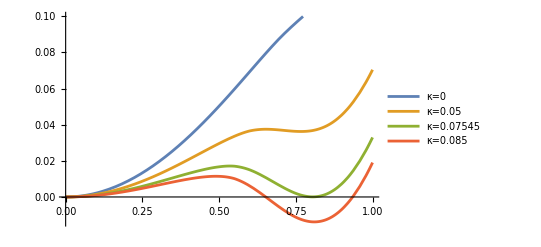

```mathematica
a=Interpolation[Transpose[{mag,EnergyPlot[[1]]}]]
b=Interpolation[Transpose[{mag,EnergyPlot[[2]]}]]
c=Interpolation[Transpose[{mag,EnergyPlot[[3]]}]]
d=Interpolation[Transpose[{mag,EnergyPlot[[4]]}]]

labels=Row[{"κ=",#}]&/@kappa;
Plot[{a[x],b[x],c[x],d[x]},{x,0,1},PlotLegends->labels]
```

# Introducing magnetisation equation

NIntegrate::zeroregion: Integration region {{0,0.6046},{2.0944,2.0943951023931830135357498742720361451605558517630551677423528245}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.05805,1.2092},{2.0944,2.0943951023931830135357498742720361451605558517630551677423528245}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

$Aborted

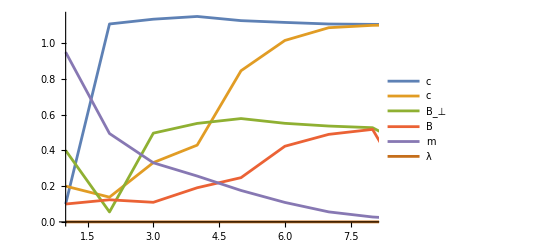

Final MFT Parameters:c_⊥ =1.10552, c_z=1.10005, B_⊥=0.527145TraditionalForm`0.517716, M=0.0356988, m=0.0274606, λ=0

```mathematica
loop=20;
Clear[cp];
Clear[cz];

cp= ConstantArray[0.1,loop];
cz = ConstantArray[0.2,loop];
bp=ConstantArray[0.4,loop];
bz=ConstantArray[0.1,loop];
m=ConstantArray[0.95,loop];
l=ConstantArray[0,loop];
P1=0;
P=0;
K1=0.1;
For[i=1,i<loop,i++,

final=i;
m[[i+1]]=(1/2)*(1/(2*(8*(Pi)^2/(3*Sqrt[3]))))* (NIntegrate[FM[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FM [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FM[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBp [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FBp[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FBz[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+
NIntegrate[FBz[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FA1[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FA1[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FA1[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FA2[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3}]+
NIntegrate[FA2[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3}]+NIntegrate[FA2[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3}]);

];



ListLinePlot[{cp,cz,bp,bz,m,l},PlotLegends->{"c","c","B_⊥","B","m","λ"},PlotRange->{{1,final},Automatic}]
Print["Final MFT Parameters:","c_⊥ =",cp[[final]] ,", c_z=",cz[[final]],", B_⊥=", bp[[final]],"TraditionalForm`", bz[[final]], ", M=", m[[final]]*(3K1*(1+P1)+1+P),", m=", m[[final]], ", λ=", l[[final]]]
z=final-1;
(*Print["Penultimate MFT Parameters:","c_⊥ =",cp[[z]] ,", c_z=",cz[[z]] ,", B_⊥=", bp[[z]],"TraditionalForm`", bz[[z]], ", M=", m[[z]]*(3K1*(1+P1)+1+P),", m=", m[[z]], ", λ=", l[[z]]]*)
```

We find that it is difficult to find the magnetisation while using the minimising magnetisation value.

# Bisection of QSL to AFM phase change:

```mathematica
cpi=1;
czi=1;
bpi=0.5;
bzi=0.5;
li=0;
loop=10;
li=0;
P1=0;
P=1.3;
loop=10;
(*Bisection*)
BS=10;(*Bisection Counter*)
Kmin=0;
Kmax=0.1;

For[b=1,b<=BS,b++, (*Loop to bisect*)

K1=(Kmax+Kmin)/2;
mag = Join[{0},Range[0.7,0.9,.01]];

(*Start calculating Energy for different m *)
For[k=1,k<=Length[mag],k++,(*Loop over m values*) 
cp= ConstantArray[cpi,loop];
cz = ConstantArray[czi,loop];
bp=ConstantArray[bpi,loop];
bz=ConstantArray[bzi,loop];
m=ConstantArray[mag[[k]],loop];
l=ConstantArray[0,loop];

(*Start MFT calc*)
For[i=1,i<loop,i++,
final=i;
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FBp [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FBp[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FBz[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+
NIntegrate[FBz[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FA1[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FA1[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FA1[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FA2[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FA2[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FA2[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

];
(*End MFT calc*)

If[mag[[k]]==0,
 Em0=Energy [P1,P,K1,cp[[final]],cz[[final]],bp[[final]],bz[[final]],0,0]
];

(*IF E-E_0<0 break loop and bisect*)
Energyval1 = Energy [P1,P,K1,cp[[final]],cz[[final]],bp[[final]],bz[[final]], mag[[k]]*(3K1*(1+P1)+1+P),0];

(*BISECTION*)
If[mag[[k]]>0, 
If[(Energyval1-Em0)<0,
Kmax=K1];
If[(Energyval1-Em0)<0,
k=100]
];


];(*end loop over m values*) 
If[Kmax!=K1,Kmin = K1]

];
```

kappa=0.05

kappa=0.025

kappa=0.0125

kappa=0.00625

kappa=0.009375

kappa=0.0078125

kappa=0.00703125

kappa=0.00664063

kappa=0.00683594

kappa=0.00673828

# Phase boundary:

```mathematica
cpi=1;
czi=1;
bpi=0.5;
bzi=0.5;
li=0;
li=0;
P1=0;
loop=10;
(*Bisection*)
BS=10;(*Bisection Counter*)


rho = Range[0,1.2,0.1]
Phaseboundary = ConstantArray[0,Length[rho]]

For[c=1,c<=Length[rho],c++,(*Loop over rho values*)

P=rho[[c]];
Kmin=0;
Kmax=0.1;

For[b=1,b<=BS,b++, (*Loop to bisect*)

K1=(Kmax+Kmin)/2;
mag = Join[{0},Range[0.7,0.95,.01]];

(*Start calculating Energy for different m *)
For[k=1,k<=Length[mag],k++,(*Loop over m values*) 
cp= ConstantArray[cpi,loop];
cz = ConstantArray[czi,loop];
bp=ConstantArray[bpi,loop];
bz=ConstantArray[bzi,loop];
m=ConstantArray[mag[[k]],loop];
l=ConstantArray[0,loop];

(*Start MFT calc*)
For[i=1,i<loop,i++,
final=i;
cp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FBp[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FBp [kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FBp[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

cz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FBz[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FBz[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+
NIntegrate[FBz[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

bp[[i+1]] = (1/2)*(1/(8*(Pi)^2/(3*Sqrt[3])))* (NIntegrate[FA1[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FA1[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FA1[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

bz[[i+1]] =1/(8*(Pi)^2/(3*Sqrt[3]))* (NIntegrate[FA2[kx,ky,i],{kx,-2*Pi/(3Sqrt[3]),2*Pi/(3Sqrt[3])},{ky,-2*Pi/3,2*Pi/3},PrecisionGoal->5]+
NIntegrate[FA2[kx,ky,i],{kx,2*Pi/(3Sqrt[3]),4*Pi/(3Sqrt[3])},{ky,Sqrt[3]*kx-4*Pi/3,-Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]+NIntegrate[FA2[kx,ky,i],{kx,-4*Pi/(3Sqrt[3]),-2*Pi/(3Sqrt[3])},{ky,-Sqrt[3]*kx-4*Pi/3,Sqrt[3]*kx+4*Pi/3},PrecisionGoal->5]);

];
(*End MFT calc*)

If[mag[[k]]==0,
 Em0=Energy [P1,P,K1,cp[[final]],cz[[final]],bp[[final]],bz[[final]],0,0]
];

(*IF E-E_0<0 break loop and bisect*)
Energyval1 = Energy [P1,P,K1,cp[[final]],cz[[final]],bp[[final]],bz[[final]], mag[[k]]*(3K1*(1+P1)+1+P),0];

(*BISECTION*)
If[mag[[k]]>0, 
If[(Energyval1-Em0)<0,
Kmax=K1];
If[(Energyval1-Em0)<0,
k=100]
];


];(*end loop over m values*) 
If[Kmax!=K1,Kmin = K1]

];
Phaseboundary[[c]] = K1;
]
```

I have stored various phase boundary points for different

```mathematica
rho={0.,0.1,0.2,0.30000000000000004,0.4,0.5,0.6000000000000001,0.7000000000000001,0.8,0.9,1.,1.1,1.2};
(*rhobar=0*)
kappa={0.07548828125000001,0.06767578125000001,0.059667968749999994,0.051660156250000006,0.04404296875,0.03681640625000001,0.03017578125,0.024121093750000003,0.01904296875,0.014941406249999999,0.01181640625,0.009667968750000002,0.00810546875};
(*rhobar=0.4*)
kappa2 ={0.05126953125000001,0.04599609375,0.04052734375000001,0.03505859375,0.029980468749999996,0.025097656250000003,0.02060546875,0.01669921875,0.013183593750000002,0.010449218750000001,0.00830078125,0.00673828125,0.00576171875};
(*rhobar=0.8*)
kappa3={0.038964843750000006,0.03486328125,0.03076171875,0.026660156250000004,0.022753906250000004,0.01904296875,0.01572265625,0.01259765625,0.010058593750000002,0.00791015625,0.00634765625,0.005175781250000001,0.00439453125};
(*rhobar=0.2*)
kappa4={0.059667968749999994,0.05322265625000001,0.04677734375,0.04052734375000001,0.034472656250000004,0.02880859375,0.02353515625,0.01904296875,0.01513671875,0.01201171875,0.009472656250000001,0.00791015625,0.006542968750000001};
kappa5={0.043261718750000004,0.03857421875000001,0.03388671875,0.02939453125,0.025097656250000003,0.02099609375,0.017285156250000003,0.01396484375,0.01103515625,0.00869140625,0.007128906250000001,0.00576171875,0.00478515625};
```

Interpolating across the phase boundary points to find the phase transition curve.

```mathematica
f=Interpolation[Transpose[{kappa,rho}]];
g=Interpolation[Transpose[{kappa2,rho}]];
h=Interpolation[Transpose[{kappa3,rho}]];
i1=Interpolation[Transpose[{kappa4,rho}]];
```

InterpolatingFunction::dmval: Input value {8.17143×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

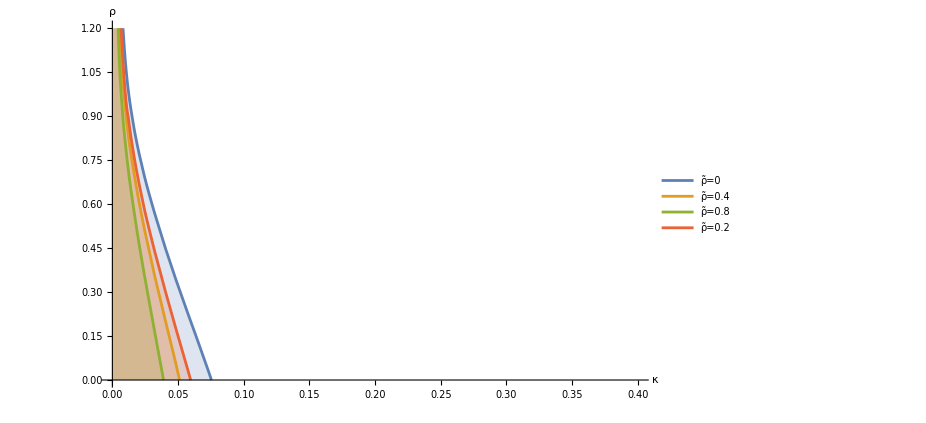

```mathematica
Plot[{f[x],g[x],h[x],i1[x]},{x,0,0.4},Filling->Bottom,PlotRange->{0,1.2},PlotLegends->{"ρ̃=0","ρ̃=0.4","ρ̃=0.8","ρ̃=0.2"},AxesLabel->{"κ","ρ"}]
```